# Model of nonlinear noise in fiber links

I suspect there is a phenomenon of secular terms in the perturbation theory of the non linear shrodinger equation. This is because the equation represents something like a set of coupled and self coupled unharmonic oscillators.
The equation is
ⅈ(∂u)/(∂z)-1/2 β''(∂^2 u)/(∂t^2)+γ|u|^2 u==0
It is useful to note that the equation can be “derived” from a lagrangian density
ℒ=1/2 γ|u|^2|u|^2+ⅈu^*(∂u)/(∂z)+1/2 β''(∂u)/(∂t)(∂u^*)/(∂t)
and an associated hamiltonian density
ℋ=1/2 β''(∂u)/(∂t)(∂u^*)/(∂t)-1/2 γ|u|^2|u|^2-ⅈu^*(∂u)/(∂z)
This gives a hamiltonian
H=∫dz(1/2 β''(∂u)/(∂t)(∂u^*)/(∂t)-1/2 γ|u|^2|u|^2-ⅈu^*(∂u)/(∂z))
Whose derivative in time is:
(∂H)/(∂t)=∫dz(1/2 β''(∂^2 u)/(∂t^2)(∂u^*)/(∂t)+1/2 β''(∂u)/(∂t)(∂^2 u^*)/(∂t^2)-ⅈ(∂u^*)/(∂t)(∂u)/(∂z)-ⅈu^*(∂^2 u)/(∂z∂t)-γ|u|^2(∂u)/(∂t)-γ|u|^2(∂u^*)/(∂t))
Using the equation
ⅈ(∂u)/(∂z)+γ|u|^2 u==1/2 β''(∂^2 u)/(∂t^2)
-ⅈ(∂u^*)/(∂z)+γ|u|^2 u^*==1/2 β''(∂^2 u^*)/(∂t^2)
(∂H)/(∂t)=∫dz(ⅈ(∂u)/(∂z)(∂u^*)/(∂t)+γ|u|^2 u(∂u^*)/(∂t)-ⅈ(∂u^*)/(∂z)(∂u)/(∂t)+γ|u|^2 u^*(∂u)/(∂t)-ⅈ(∂u^*)/(∂t)(∂u)/(∂z)-ⅈu^*(∂^2 u)/(∂z∂t)-γ|u|^2(∂u)/(∂t)-γ|u|^2(∂u^*)/(∂t))=
∫dz(-ⅈ(∂u^*)/(∂z)(∂u)/(∂t)-ⅈu^*(∂^2 u)/(∂z∂t))=∫dz∂/(∂z)(-ⅈu^*(∂u)/(∂t))=-ⅈu^*(∂u)/(∂t)|_boundary
We get that the Hamiltonian is not conserved but can be conserved in special conditions:

```mathematica
order=1;
u[z_,t_]:>SeriesData[γ,0,Table[a[i][z,t],{i,order}],0,order+1,1]

DSolve[ⅈ D[u[z,t],z]-1/2 β D[u[z,t],{t,2}]+γ u[z,t]^3==0,u,{z,t}]
```

u[z_,t_]:>SeriesData[γ,0,Table[a[i][z,t],{i,order}],0,order+1,1]

DSolve[γ u[z,t]^3-1/2 β u^(0,2)[z,t]+ⅈ u^(1,0)[z,t]==0,u,{z,t}]

```mathematica
Simplify[ⅈ D[u[z,t],z]-1/2 β D[u[z,t],{t,2}]+γ Abs[u[z,t]]^2 u[z,t]==0/.u->Function[{z,t},√P1 Sech[t/t0] ⅇ^(ⅈ γ P1 z/2)],P1>0&&t>0&&t0>0&&γ>0&&z>0]
```

(β+P1 t0^2 γ) (-3+Cosh[(2 t)/t0])==0

```mathematica
D[D[Sech[t], t], t]//Simplify
```

1/2 (-3+Cosh[2 t]) Sech[t]^3

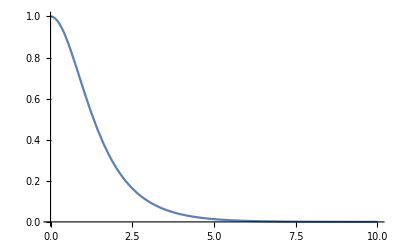

```mathematica
Plot[Sech[t],{t,0,10}]
```

## Duffing’s equation in perturbation theory

The Duffing equation is
y''+ω^2 y+4 λy^3==0
In the perturbative solution of the equation there arises secular terms. My aim here is to understand where these fundamentally come from in order to develope a new method of analyzing in advance whether they will appear and maybe a new method of doing “multiple scale analysis”.

The equation has a conserved quantity
E=1/2(y')^2+1/2 ω^2 y^2+λy^4
Which leads to the equation
E-1/2 ω^2 y^2-λy^4=1/2(y')^2
y'=√(2E-ω^2 y^2-2 λy^4)
∫dy/(√(2E-ω^2 y^2-2 λy^4))=∫dt
Which can be solved below

```mathematica
∫1/(√(2EE-ω^2 y^2-2λ y^4))ⅆy
```

-((ⅈ √(1-(4 y^2 λ)/(-ω^2+√(16 EE λ+ω^4))) √(1+(4 y^2 λ)/(ω^2+√(16 EE λ+ω^4))) EllipticF[ⅈ ArcSinh[2 y √(-λ/(-ω^2+√(16 EE λ+ω^4)))],-(-ω^2+√(16 EE λ+ω^4))/(ω^2+√(16 EE λ+ω^4))])/(2 √(2 EE-2 y^4 λ-y^2 ω^2) √(-λ/(-ω^2+√(16 EE λ+ω^4)))))

```mathematica
Limit[%,y->0]//Simplify
```

0

This integral gives a time interval. We can get one quarter of the period if we integrate ∫_0^y_max  where
E=1/2 ω^2 y_max^2+λy_max^4

```mathematica
Solve[λ x^4+ω^2/2 x^2==EE,x]
```

{{x→-1/2 √(-ω^2/λ-(√(16 EE λ+ω^4))/λ)},{x→1/2 √(-ω^2/λ-(√(16 EE λ+ω^4))/λ)},{x→-1/2 √(-ω^2/λ+(√(16 EE λ+ω^4))/λ)},{x→1/2 √(-ω^2/λ+(√(16 EE λ+ω^4))/λ)}}

so that
y_max=1/2 √(-ω^2/λ+(√(16 EE λ+ω^4))/λ)

We want to

```mathematica
∫1/(√(2EE-ω^2 y^2-2λ y^4))ⅆy/.y-> ω/(2 √λ)√(√((16 EE λ)/ω^4+1)-1)//Simplify
```

ComplexInfinity

```mathematica
Refine[Series[ω/(2 √λ)√(√((16 EE λ)/ω^4+1)-1),{λ,0,2}],ω>0]
```

(√2 √EE)/ω-(2 (√2 EE^(3/2)) λ)/ω^5+(14 √2 EE^(5/2) λ^2)/ω^9+O[λ]^(5/2)

We
∫dy/(√(2E-ω^2 y^2-2 λy^4))=∫dt

```mathematica
Solve[2EE-ω^2 y^2-2λ y^4==0,y]
```

{{y→-1/2 √(-ω^2/λ-(√(16 EE λ+ω^4))/λ)},{y→1/2 √(-ω^2/λ-(√(16 EE λ+ω^4))/λ)},{y→-1/2 √(-ω^2/λ+(√(16 EE λ+ω^4))/λ)},{y→1/2 √(-ω^2/λ+(√(16 EE λ+ω^4))/λ)}}

```mathematica
(y+1/2 √(-ω^2/λ-(√(16 EE λ+ω^4))/λ))(y-1/2 √(-ω^2/λ-(√(16 EE λ+ω^4))/λ))(y+1/2 √(-ω^2/λ+(√(16 EE λ+ω^4))/λ))(y-1/2 √(-ω^2/λ+(√(16 EE λ+ω^4))/λ))//Simplify
```

(-2 EE+2 y^4 λ+y^2 ω^2)/(2 λ)

bla

```mathematica
eq=y''[x]+ω^2 y[x]+ϵ y[x]^3==0/.y->Function[x,Cos[ω x+ϵ ϕ1[x]+ϵ^2 ϕ2[x]]]//Simplify;
```

```mathematica
eq=Series[eq,{ϵ,0,2}];
```

```mathematica
eq=Simplify[eq];
```

```mathematica
s1=DSolve[Cos[x ω]^3-2 ω Cos[x ω] ϕ1'[x]-Sin[x ω] ϕ1''[x]==0,ϕ1,x][[1,1]];
```

```mathematica
eq=Simplify[ReplaceAll[eq,s1]]
```

(-(Cos[x ω] (3+Cos[2 x ω]+(-2+8 ω C[1]) Csc[x ω]^2)^2)/(64 ω^2)+1/(512 ω^2)(7-32 ω C[1]+3 Cos[2 x ω]-3 Cos[4 x ω]+Cos[6 x ω]) Csc[x ω]^4 ((-9+32 ω C[1]) Cos[x ω]+Cos[3 x ω]-4 ω (3 x+8 ω C[2]) Sin[x ω])-2 ω Cos[x ω] ϕ2'[x]-Sin[x ω] ϕ2''[x]) ϵ^2+O[ϵ]^3==0

```mathematica
DSolve[-(Cos[x ω] (3+Cos[2 x ω]+(-2+8 ω C[1]) Csc[x ω]^2)^2)/(64 ω^2)+1/(512 ω^2)(7-32 ω C[1]+3 Cos[2 x ω]-3 Cos[4 x ω]+Cos[6 x ω]) Csc[x ω]^4 ((-9+32 ω C[1]) Cos[x ω]+Cos[3 x ω]-4 ω (3 x+8 ω C[2]) Sin[x ω])-2 ω Cos[x ω] ϕ2'[x]-Sin[x ω] ϕ2''[x]==0,ϕ2,x]
```

```mathematica
s2={{ϕ2->Function[{x},ⅇ^(-x √(-ω^2)) C[3] Csc[x ω]+(ⅇ^(x √(-ω^2)) C[4] Csc[x ω])/(2 √(-ω^2))+1/(2 √(-ω^2))ⅇ^(-x √(-ω^2)) Csc[x ω] (2 √(-ω^2) ∫_1^x (-(11 ⅇ^(√(-ω^2) K[1]) √(-ω^2) C[2] Csc[ω K[1]]^3)/(64 ω^2)+(ⅇ^(√(-ω^2) K[1]) √(-ω^2) C[1] C[2] Csc[ω K[1]]^3)/ω-(369 ⅇ^(√(-ω^2) K[1]) √(-ω^2) Cot[ω K[1]] Csc[ω K[1]]^3)/(4096 ω^4)+(45 ⅇ^(√(-ω^2) K[1]) √(-ω^2) C[1] Cot[ω K[1]] Csc[ω K[1]]^3)/(64 ω^3)-(3 ⅇ^(√(-ω^2) K[1]) √(-ω^2) C[1]^2 Cot[ω K[1]] Csc[ω K[1]]^3)/(2 ω^2)-(3 ⅇ^(√(-ω^2) K[1]) √(-ω^2) Cos[3 ω K[1]] Csc[ω K[1]]^4)/(1024 ω^4)+(3 ⅇ^(√(-ω^2) K[1]) √(-ω^2) C[1] Cos[3 ω K[1]] Csc[ω K[1]]^4)/(64 ω^3)+(3 ⅇ^(√(-ω^2) K[1]) √(-ω^2) Cos[5 ω K[1]] Csc[ω K[1]]^4)/(512 ω^4)-(ⅇ^(√(-ω^2) K[1]) √(-ω^2) C[1] Cos[5 ω K[1]] Csc[ω K[1]]^4)/(64 ω^3)-(57 ⅇ^(√(-ω^2) K[1]) √(-ω^2) Cos[7 ω K[1]] Csc[ω K[1]]^4)/(8192 ω^4)+(ⅇ^(√(-ω^2) K[1]) √(-ω^2) C[1] Cos[7 ω K[1]] Csc[ω K[1]]^4)/(64 ω^3)+(3 ⅇ^(√(-ω^2) K[1]) √(-ω^2) Cos[9 ω K[1]] Csc[ω K[1]]^4)/(8192 ω^4)-(33 ⅇ^(√(-ω^2) K[1]) √(-ω^2) Csc[ω K[1]]^3 K[1])/(512 ω^3)+(3 ⅇ^(√(-ω^2) K[1]) √(-ω^2) C[1] Csc[ω K[1]]^3 K[1])/(8 ω^2)-(3 ⅇ^(√(-ω^2) K[1]) √(-ω^2) C[2] Csc[ω K[1]]^4 Sin[3 ω K[1]])/(32 ω^2)-(9 ⅇ^(√(-ω^2) K[1]) √(-ω^2) Csc[ω K[1]]^4 K[1] Sin[3 ω K[1]])/(256 ω^3)+(ⅇ^(√(-ω^2) K[1]) √(-ω^2) C[2] Csc[ω K[1]]^4 Sin[5 ω K[1]])/(16 ω^2)+(3 ⅇ^(√(-ω^2) K[1]) √(-ω^2) Csc[ω K[1]]^4 K[1] Sin[5 ω K[1]])/(128 ω^3)-(ⅇ^(√(-ω^2) K[1]) √(-ω^2) C[2] Csc[ω K[1]]^4 Sin[7 ω K[1]])/(64 ω^2)-(3 ⅇ^(√(-ω^2) K[1]) √(-ω^2) Csc[ω K[1]]^4 K[1] Sin[7 ω K[1]])/(512 ω^3))ⅆK[1]+ⅇ^(2 x √(-ω^2)) ∫_1^x (-11/32 ⅇ^(-√(-ω^2) K[2]) C[2] Csc[ω K[2]]^3+2 ⅇ^(-√(-ω^2) K[2]) ω C[1] C[2] Csc[ω K[2]]^3-(369 ⅇ^(-√(-ω^2) K[2]) Cot[ω K[2]] Csc[ω K[2]]^3)/(2048 ω^2)+(45 ⅇ^(-√(-ω^2) K[2]) C[1] Cot[ω K[2]] Csc[ω K[2]]^3)/(32 ω)-3 ⅇ^(-√(-ω^2) K[2]) C[1]^2 Cot[ω K[2]] Csc[ω K[2]]^3-(3 ⅇ^(-√(-ω^2) K[2]) Cos[3 ω K[2]] Csc[ω K[2]]^4)/(512 ω^2)+(3 ⅇ^(-√(-ω^2) K[2]) C[1] Cos[3 ω K[2]] Csc[ω K[2]]^4)/(32 ω)+(3 ⅇ^(-√(-ω^2) K[2]) Cos[5 ω K[2]] Csc[ω K[2]]^4)/(256 ω^2)-(ⅇ^(-√(-ω^2) K[2]) C[1] Cos[5 ω K[2]] Csc[ω K[2]]^4)/(32 ω)-(57 ⅇ^(-√(-ω^2) K[2]) Cos[7 ω K[2]] Csc[ω K[2]]^4)/(4096 ω^2)+(ⅇ^(-√(-ω^2) K[2]) C[1] Cos[7 ω K[2]] Csc[ω K[2]]^4)/(32 ω)+(3 ⅇ^(-√(-ω^2) K[2]) Cos[9 ω K[2]] Csc[ω K[2]]^4)/(4096 ω^2)-3/16 ⅇ^(-√(-ω^2) K[2]) C[2] Csc[ω K[2]]^4 Sin[3 ω K[2]]+1/8 ⅇ^(-√(-ω^2) K[2]) C[2] Csc[ω K[2]]^4 Sin[5 ω K[2]]-1/32 ⅇ^(-√(-ω^2) K[2]) C[2] Csc[ω K[2]]^4 Sin[7 ω K[2]]+1/(256 ω)3 ⅇ^(-√(-ω^2) K[2]) Csc[ω K[2]]^3 K[2] (-11+64 ω C[1]-6 Csc[ω K[2]] Sin[3 ω K[2]]+4 Csc[ω K[2]] Sin[5 ω K[2]]-Csc[ω K[2]] Sin[7 ω K[2]]))ⅆK[2])]}}[[1,1]];
```

```mathematica
eq=Simplify[ReplaceAll[eq,s2]]
```

O[ϵ]^3==0